# A simple introduction to option pricing ... without too much math

Option pricing is a hard topic. It requires advanced mathematical training which means that the topic is not very accessible. 

This introduction is based on the 1979 paper Option Pricing: A simplified approach. My goal with this article is to give you an intuition to how options can be priced without too much math. If you find the topic interesting, go read the paper.

### Part 1: The easy case

Let’s imagine the following simplistic scenario. There is stock whose price is S = $50 and at the end of the day it can be either $25 or $100 and there is a call with strike price K = $50. Finally, the interest free rate is 25%.
Our goal is going to be to find the price of that call with strike of K = $50 .

What values can the stock take? Let’s represent this with a diagram.

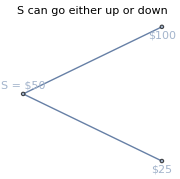

```mathematica
TreePlot[
{
"S = $50"->"$25","S = $50"->"$100"
}, 
Left, 
VertexLabels->"Name",
ImageSize->Small,
PlotLabel->"S can go either up or down"
]
```

Finally, what  values can the call take at expiration? Remember that at expiration a call option is worth Max(S-K). Let C denote the price of the call today.

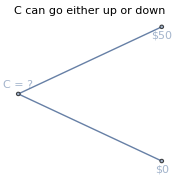

```mathematica
TreePlot[
{
"C = ?"->"$0","C = ?"->"$50"
}, 
Left, 
VertexLabels->"Name",
ImageSize->Small,
PlotLabel->"C can go either up or down"
]
```

### The “trick”

In order to find the value of C, we are going to create a position by combining stocks and calls whose value will be the same whether the stock goes up to $100 or down to $25.

Let’s construct the position:

Write 3 calls at C each
Buy 2 shares at $50 each 
Borrow $40 at 25% to be paid at the end of the period

How much cash will we hold in our pockets today with this position?
By writing the 3 calls we generate an income of 3C, buying the 2 calls we need to pay 2*$50 and finally by borrowing $40, we get an additional $40 (which we will need to pay later). This gives us the following formula:

3C - 2*$50 + $40

Let’s see how our portfolio’s value will change if the stock goes up to $100:
The short calls will be worth $50 each, so this means we will have to pay out $150.
The stock will move to $100, meaning our stock position will be worth $200.
We will need to pay back the $40 plus interest of 25%, totalling $50.

-$150 + $200 - $50 = $0

And finally, let’s see how our portfolio’s value will change if the stock goes down to $25:
The short calls will be worth $0 each.
The stock will move to $25, meaning our stock position will be worth $50.
We will need to pay back the $40 plus interest of 25%, totalling $50.

$0 + $50 - $50 = $0

Let’s summarize this in a diagram:

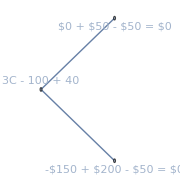

```mathematica
TreePlot[
{
"3C - 100 + 40"->"-$150 + $200 - $50 = $0",
"3C - 100 + 40"->"$0 + $50 - $50 = $0"
}, 
Left, 
VertexLabels->"Name",
ImageSize->Small
]
```

There’s one very important thing to notice about this diagram: The position is worth $0 whether the stock goes up or down. So what is the value of 3C - 100 + 40  then? Let’s consider a few cases:

Imagine that the value of 3C - 100 + 40 was > 0. Then we have created a position that is worth something today, but always goes to zero. What could we do if we found such a situation in the markets? We could make a riskless profit. The same is true about the reverse case, i.e. if 3C - 100 + 40 < 0.

If we assume that the market we’re trading in is an “efficient market”, then these kind of risk-free profit opportunities will disappear quickly, which means the only possibility is that our position is also worth $0 today. This gives us then the following equation:

3C - $100 + $40 = 0

Which solving for C gives:

C = $20

### Summary

A stock has a value of $50 today and can go to either $25 or $100.

We want to find the value of a call with strike of $50 expiring tomorrow.

We created a position that was worth $0 whether the stock went up or down.

We argued that if the position was always worth $0 at expiration, it must have been worth $0 today.

### Part 2: Generalizing the easy case

Let’s take the learnings from Part 1 and generalize a bit. Let’s introduce some terminology:

S is the price of the stock today.

uS is the price of the stock at expiration when the stock rises. For example if the stock rose by 5% then u would be (1+5%) i.e. uS = S(1+0.05).

dS the price of the stock at expiration when the stock falls.

q the probability of the stock rising.

r the risk free rate plus one. For example if the interest free rate is 2%, then r = (1+0.02).

C the present value of a call with strike K.

C_u=Max(uS-K,0) the value of the call when the stock rises.

C_d=Max(dS-K,0) the value of the call when the stock falls.

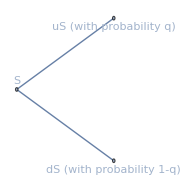

```mathematica
TreePlot[
{
"S"->"dS (with probability 1-q)",
"S"->"uS (with probability q)"
}, 
Left, 
VertexLabels->"Name",
ImageSize->Small
]
```

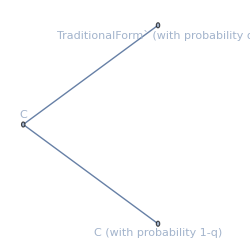

```mathematica
TreePlot[
{
"C"->"C (with probability 1-q)",
"C"->"TraditionalForm` (with probability q)"
}, 
Left, 
VertexLabels->"Name",
ImageSize->250
]
```

Now let’s form the following portfolio:

Buy Δ shares of stock, meaning we need to pay -ΔS today.
Borrow B at the interest free rate. We will need to repay rB in the next period.

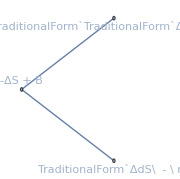

```mathematica
TreePlot[
{
"-ΔS + B"->"TraditionalForm`ΔdS\  - \ rB",
"-ΔS + B"->"TraditionalForm`TraditionalForm`ΔuS\  - \ rB"
}, 
Left, 
VertexLabels->"Name",
ImageSize->Small
]
```

### The “trick”

Notice that we are free to pick any combination of Δ and B, so let’s choose them such that they satisfy the following conditions:

ΔuS-rB = C_u 

ΔdS-rB = C_d

This gives us a system of two linear equations with 2 unknowns (Δ,B) which has the following solutions:

Δ=(C_d - C_u)/(S(d-u))

B=(C_d u - C_u d)/(r (d-u))